# Roller Coaster Creator

Julia Gensheimer and Valerie Richmond

## 2D Splines

The logic and calculations behind the spline code came from a document sent to us by Dr. Ernst. We found this was a better option than a large 6th degree polynomial.
Reference: The natural cubic spline
From: Calculus and Mathematica
Authors: Bill Davis, Horacio Porta, and Jerry Uhl (1999)

```mathematica
(*updateSpline generates the roller coaster track.*)
updateSpline[]:=Module[{},
(*List of adjustable points are updated to their new coordinates depending on how the user adjusts the track*)
ptLst:={{-1000000, 1500},{xLeftBound,yLeftBound},{ptLstNoEnd[[1,1]], ptLstNoEnd[[1,2]]},{ptLstNoEnd[[2,1]],ptLstNoEnd[[2,2]]},{ptLstNoEnd[[3,1]],ptLstNoEnd[[3,2]]},{ptLstNoEnd[[4,1]],ptLstNoEnd[[4,2]]},{ptLstNoEnd[[5,1]],ptLstNoEnd[[5,2]]},{xRightBound,yRightBound},{1000000,1500}};

(*Sort the list of points so that the x[k] increase as k increases*)
Clear[x,y,K];
ptList=N[Sort[ptList]];
x[k_]:=ptLst[[k,1]];
y[k_]:=ptLst[[k,2]];
K=Length[ptLst]; (*K is equal to 7*)

(*f[k,x] is the cubic we will run from {x[k], y[k]} to {x[k + 1], y[k + 1]}*)
Clear[f,a,b,c,d,k];
f[k_,x_]:=a[k] x^3+b[k] x^2+c[k]x+d[k];
(*k runs from k=1 to k=6, so we have 6 cubics*)

(*Equations for natural cubic spline*)
eqn1=Table[f[k,x[k]]==y[k],{k,1,K-1}];
eqn2=Table[f[k,x[k+1]]==y[k+1],{k,1,K-1}];
(*need derivatives for smoothness at the knots*)
eqn3=Table[(D[f[k,x],x]==D[f[k-1,x],x])/.x-> x[k],{k,2,K-1}];
(*set second derivatives equal to 0 at endpoints*)
eqn4=Table[(D[f[k,x],{x,2}]==D[f[k-1,x],{x,2}])/.x-> x[k],
{k,2,K-1}];
eqn5={(D[f[1,x],{x,2}]/.x->x[1])==0, (D[f[K-1,x],{x,2}]/.x-> x[K])==0};

(*Join all of the equations*)
allEqn=Join[eqn1,eqn2,eqn3,eqn4,eqn5];
(*Solve for coefficients*)
coeffLst=Flatten[Table[{a[k],b[k],c[k],d[k]},{k,K-1}]];
coefs=Chop[Solve[allEqn,coeffLst][[1]]];

(*Substitute the coefficients into the formulas to define the spline function*)
Clear[spline,t,k,thisg];
thisg[k_,t_]:=f[k,t]/.coefs;
Do[With[{m=k,n=k+1},spline[t_]:=thisg[m,t]/;x[m]≤t<x[n]],{k,K-1}];
]
```

```mathematica
Do[With[{m=k,n=k+1},spline[t_]:=thisg[m,t]/;x[m]≤t<x[n]],{k,6}];
```

```mathematica
(*Create a plot of the points*)
pointPlot=ListPlot[ptLst,PlotStyle-> {Red,PointSize[0.025]}];
```

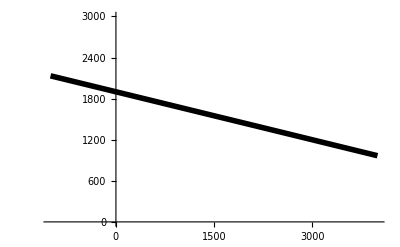

```mathematica
(*Graph the spline function*)
splinePlot=Plot[spline[t],{t,-1000,4000}, AspectRatio-> 1/GoldenRatio, PlotRange-> {0,3000},PlotStyle->{Black,{Thickness[0.01]}},Axes->True]
```

## 3D Splines

```mathematica
sliderValue=1;  (*default starting "t" variable for the parametric plot*)
```

```mathematica
updateSplines3D[]:=Module[{},
(*List of adjustable points are updated to their new coordinates depending on how the user adjusts the track*)

If[SameQ[Head[xyzList],Dynamic],
(*If it is dynamic, add the 1 to front*)
(*A part 1 specification is made if the list is dynamic(adjusted by the user on the panels) when separating the xyz list into three lists for the parametric plot*)
xPtLst={{1,xLeftBound},{2,xyzList[[1,1,1]]},{3,xyzList[[1,2,1]]},{4,xyzList[[1,3,1]]},{5,xyzList[[1,4,1]]},{6,xyzList[[1,5,1]]},{7,xRightBound}};
yPtLst={{1,yLeftBound},{2,xyzList[[1,1,2]]},{3,xyzList[[1,2,2]]},{4,xyzList[[1,3,2]]},{5,xyzList[[1,4,2]]},{6,xyzList[[1,5,2]]},{7,yRightBound}};
zPtLst={{1,zLeftBound},{2,xyzList[[1,1,3]]},{3,xyzList[[1,2,3]]},{4,xyzList[[1,3,3]]},{5,xyzList[[1,4,3]]},{6,xyzList[[1,5,3]]},{7,zRightBound}},
(*If it's not, use a normal part*)
xPtLst={{1,xLeftBound},{2,xyzList[[1,1]]},{3,xyzList[[2,1]]},{4,xyzList[[3,1]]},{5,xyzList[[4,1]]},{6,xyzList[[5,1]]},{7,xRightBound}};
yPtLst={{1,yLeftBound},{2,xyzList[[1,2]]},{3,xyzList[[2,2]]},{4,xyzList[[3,2]]},{5,xyzList[[4,2]]},{6,xyzList[[5,2]]},{7,yRightBound}};
zPtLst={{1,zLeftBound},{2,xyzList[[1,3]]},{3,xyzList[[2,3]]},{4,xyzList[[3,3]]},{5,xyzList[[4,3]]},{6,xyzList[[5,3]]},{7,zRightBound}}
];
(*Separates the list into x y and z lists normally if the list is not dynamic, meaning it was changed by the click of a button*)
(*Sort the list of points so that the x[k] increase as k increases*)
Clear[xX,xY,yX,yY,zX,zY,K,k];
xPtLst=N[Sort[xPtLst]];
xX[k_]:=xPtLst[[k,1]];
xY[k_]:=xPtLst[[k,2]];
K=Length[xPtLst]; (*K is 7 which is the same value for xPtLst, yPtLst, and zPtLst*)

Clear[k];
yPtLst=N[Sort[yPtLst]];
yX[k_]:=yPtLst[[k,1]];
yY[k_]:=yPtLst[[k,2]];

Clear[k];
zPtLst=N[Sort[zPtLst]];
zX[k_]:=zPtLst[[k,1]];
zY[k_]:=zPtLst[[k,2]];

(*FIRST FUNCTION INFO*)
Clear[firstF,a,b,c,d,k,x];
firstF[k_,x_]:=a[k] x^3+b[k] x^2+c[k]x+d[k];
firstEqn1=Table[firstF[k,xX[k]]==xY[k],{k,1,K-1}];
firstEqn2=Table[firstF[k,xX[k+1]]==xY[k+1],{k,1,K-1}];
firstEqn3=Table[(D[firstF[k,x],x]==D[firstF[k-1,x],x])/.x-> xX[k],{k,2,K-1}];
(*set second derivatives equal to 0 at endpoints*)
firstEqn4=Table[(D[firstF[k,x],{x,2}]==D[firstF[k-1,x],{x,2}])/.x-> xX[k],
{k,2,K-1}];
firstEqn5={(D[firstF[1,x],{x,2}]/.x->xX[1])==0, (D[firstF[K-1,x],{x,2}]/.x-> xX[K])==0};
firstAllEqn=Join[firstEqn1,firstEqn2,firstEqn3,firstEqn4,firstEqn5];
firstCoeffLst=Flatten[Table[{a[k],b[k],c[k],d[k]},{k,K-1}]];
firstCoefs=Chop[Solve[firstAllEqn,firstCoeffLst][[1]]];
Clear[splineX,t,k,q,m,t];
q[k_,t_]:=firstF[k,t]/.firstCoefs;
Do[With[{m=k,n=k+1},splineX[t_]:=q[m,t]/;xX[m]≤t<xX[n]],{k,K-1}];

(*SECOND FUNCTION INFO*)
Clear[secondF,e,m,n,o,k,x];
secondF[k_,x_]:=e[k] x^3+m[k] x^2+n[k]x+o[k];
secondEqn1=Table[secondF[k,yX[k]]==yY[k],{k,1,K-1}];
secondEqn2=Table[secondF[k,yX[k+1]]==yY[k+1],{k,1,K-1}];
secondEqn3=Table[(D[secondF[k,x],x]==D[secondF[k-1,x],x])/.x-> yX[k],{k,2,K-1}];
(*set second derivatives equal to 0 at endpoints*)
secondEqn4=Table[(D[secondF[k,x],{x,2}]==D[secondF[k-1,x],{x,2}])/.x-> yX[k],
{k,2,K-1}];
secondEqn5={(D[secondF[1,x],{x,2}]/.x->yX[1])==0, (D[secondF[K-1,x],{x,2}]/.x-> yX[K])==0};
secondAllEqn=Join[secondEqn1,secondEqn2,secondEqn3,secondEqn4,secondEqn5]; 
secondCoeffLst=Flatten[Table[{e[k],m[k],n[k],o[k]},{k,K-1}]];
secondCoefs=Chop[Solve[secondAllEqn,secondCoeffLst][[1]]];
Clear[splineY,t,k,qq];
qq[k_,t_]:=secondF[k,t]/.secondCoefs;
Do[With[{m=k,n=k+1},splineY[t_]:=qq[m,t]/;yX[m]≤t<yX[n]],{k,K-1}];


(*THIRD FUNCTION STUFF*)
Clear[thirdF,p,r,s,u,k,x,m,n];
thirdF[k_,x_]:=p[k] x^3+r[k] x^2+s[k]x+u[k];
thirdEqn1=Table[thirdF[k,zX[k]]==zY[k],{k,1,K-1}];
thirdEqn2=Table[thirdF[k,zX[k+1]]==zY[k+1],{k,1,K-1}];
thirdEqn3=Table[(D[thirdF[k,x],x]==D[thirdF[k-1,x],x])/.x-> zX[k],{k,2,K-1}];
(*set second derivatives equal to 0 at endpoints*)
thirdEqn4=Table[(D[thirdF[k,x],{x,2}]==D[thirdF[k-1,x],{x,2}])/.x-> zX[k],
{k,2,K-1}];
thirdEqn5={(D[thirdF[1,x],{x,2}]/.x->zX[1])==0, (D[thirdF[K-1,x],{x,2}]/.x-> zX[K])==0};
thirdAllEqn=Join[thirdEqn1,thirdEqn2,thirdEqn3,thirdEqn4,thirdEqn5];
thirdCoeffLst=Flatten[Table[{p[k],r[k],s[k],u[k]},{k,K-1}]];
thirdCoefs=Chop[Solve[thirdAllEqn,thirdCoeffLst][[1]]];
Clear[splineZ,t,k,qqq];
qqq[k_,t_]:=thirdF[k,t]/.thirdCoefs;
Do[With[{m=k,n=k+1},splineZ[t_]:=qqq[m,t]/;zX[m]≤t<zX[n]],{k,K-1}];

 (*the display*)

Column[{

(*Display the coins and track and point dots*)
Show[ParametricPlot3D[{splineX[t],splineY[t],splineZ[t]},{t,1,7},PlotStyle->Thickness[.002],AxesLabel->{"x","y","z"}, ViewPoint->Dynamic[view],ImageSize-> Medium,Ticks->None,PlotStyle->Thick],Graphics3D[{
Dynamic[RGBColor[redDC, greenDC, blueDC]],

(*Cart*)
Rotate[Cuboid[getCartPoints3D[150,90,splineX[sliderValue],splineY[sliderValue],splineZ[sliderValue], splineX[sliderValue+.001], splineY[sliderValue+.001]]],
 (*slope of the track*)
ArcTan[(splineY[sliderValue]-splineY[sliderValue+.001])/(splineX[sliderValue]-splineX[sliderValue+.001])],

 (*displays the cuboid*)
getCartPoints3D[150,90,splineX[sliderValue],splineY[sliderValue],splineZ[sliderValue], splineX[sliderValue+.001], splineY[sliderValue+.001]][[1]]],
Purple,PointSize[Large],PointSize[Large],

(*locator and end points display*)
Point[Table[{xPtLst[[i,2]],yPtLst[[i,2]],zPtLst[[i,2]]},{i,1,Length[xPtLst]}]],Green,Point[{{xLeftBound,yLeftBound,zLeftBound},{xRightBound,yRightBound,zRightBound}}], 

 (*coin displays: as spheres*)
Yellow,Opacity[coin1opacity],Dynamic[coin13D], Opacity[coin2opacity], Dynamic[coin23D], Opacity[coin3opacity], Dynamic[coin33D]}]
, SphericalRegion->True, ContentSelectable->False]

}]];
```

```mathematica
updateSplines3DWithSupport[]:=Module[{},
If[SameQ[Head[xyzList],Dynamic],
(*If it is dynamic, add the 1 to front*)
(*A part 1 specification is made if the list is dynamic(adjusted by the user on the panels) when separating the xyz list into three lists for the parametric plot*)
xPtLst={{1,xLeftBound},{2,xyzList[[1,1,1]]},{3,xyzList[[1,2,1]]},{4,xyzList[[1,3,1]]},{5,xyzList[[1,4,1]]},{6,xyzList[[1,5,1]]},{7,xRightBound}};
yPtLst={{1,yLeftBound},{2,xyzList[[1,1,2]]},{3,xyzList[[1,2,2]]},{4,xyzList[[1,3,2]]},{5,xyzList[[1,4,2]]},{6,xyzList[[1,5,2]]},{7,yRightBound}};
zPtLst={{1,zLeftBound},{2,xyzList[[1,1,3]]},{3,xyzList[[1,2,3]]},{4,xyzList[[1,3,3]]},{5,xyzList[[1,4,3]]},{6,xyzList[[1,5,3]]},{7,zRightBound}},
(*If it's not, use a normal part*)
xPtLst={{1,xLeftBound},{2,xyzList[[1,1]]},{3,xyzList[[2,1]]},{4,xyzList[[3,1]]},{5,xyzList[[4,1]]},{6,xyzList[[5,1]]},{7,xRightBound}};
yPtLst={{1,yLeftBound},{2,xyzList[[1,2]]},{3,xyzList[[2,2]]},{4,xyzList[[3,2]]},{5,xyzList[[4,2]]},{6,xyzList[[5,2]]},{7,yRightBound}};
zPtLst={{1,zLeftBound},{2,xyzList[[1,3]]},{3,xyzList[[2,3]]},{4,xyzList[[3,3]]},{5,xyzList[[4,3]]},{6,xyzList[[5,3]]},{7,zRightBound}}
];
(*Separates the list into x y and z lists normally if the list is not dynamic, meaning it was changed by the click of a button*)
(*Sort the list of points so that the x[k] increase as k increases*)
Clear[xX,xY,yX,yY,zX,zY,K,k];
xPtLst=N[Sort[xPtLst]];
xX[k_]:=xPtLst[[k,1]];
xY[k_]:=xPtLst[[k,2]];
K=Length[xPtLst]; (*K is 7 which is the same value for xPtLst, yPtLst, and zPtLst*)

Clear[k];
yPtLst=N[Sort[yPtLst]];
yX[k_]:=yPtLst[[k,1]];
yY[k_]:=yPtLst[[k,2]];

Clear[k];
zPtLst=N[Sort[zPtLst]];
zX[k_]:=zPtLst[[k,1]];
zY[k_]:=zPtLst[[k,2]];

(*FIRST FUNCTION INFO*)
Clear[firstF,a,b,c,d,k,x];
firstF[k_,x_]:=a[k] x^3+b[k] x^2+c[k]x+d[k];
firstEqn1=Table[firstF[k,xX[k]]==xY[k],{k,1,K-1}];
firstEqn2=Table[firstF[k,xX[k+1]]==xY[k+1],{k,1,K-1}];
firstEqn3=Table[(D[firstF[k,x],x]==D[firstF[k-1,x],x])/.x-> xX[k],{k,2,K-1}];
(*set second derivatives equal to 0 at endpoints*)
firstEqn4=Table[(D[firstF[k,x],{x,2}]==D[firstF[k-1,x],{x,2}])/.x-> xX[k],
{k,2,K-1}];
firstEqn5={(D[firstF[1,x],{x,2}]/.x->xX[1])==0, (D[firstF[K-1,x],{x,2}]/.x-> xX[K])==0};
firstAllEqn=Join[firstEqn1,firstEqn2,firstEqn3,firstEqn4,firstEqn5];
firstCoeffLst=Flatten[Table[{a[k],b[k],c[k],d[k]},{k,K-1}]];
firstCoefs=Chop[Solve[firstAllEqn,firstCoeffLst][[1]]];
Clear[splineX,t,k,q,m,t];
q[k_,t_]:=firstF[k,t]/.firstCoefs;
Do[With[{m=k,n=k+1},splineX[t_]:=q[m,t]/;xX[m]≤t<xX[n]],{k,K-1}];

(*SECOND FUNCTION INFO*)
Clear[secondF,e,m,n,o,k,x];
secondF[k_,x_]:=e[k] x^3+m[k] x^2+n[k]x+o[k];
secondEqn1=Table[secondF[k,yX[k]]==yY[k],{k,1,K-1}];
secondEqn2=Table[secondF[k,yX[k+1]]==yY[k+1],{k,1,K-1}];
secondEqn3=Table[(D[secondF[k,x],x]==D[secondF[k-1,x],x])/.x-> yX[k],{k,2,K-1}];
(*set second derivatives equal to 0 at endpoints*)
secondEqn4=Table[(D[secondF[k,x],{x,2}]==D[secondF[k-1,x],{x,2}])/.x-> yX[k],
{k,2,K-1}];
secondEqn5={(D[secondF[1,x],{x,2}]/.x->yX[1])==0, (D[secondF[K-1,x],{x,2}]/.x-> yX[K])==0};
secondAllEqn=Join[secondEqn1,secondEqn2,secondEqn3,secondEqn4,secondEqn5]; 
secondCoeffLst=Flatten[Table[{e[k],m[k],n[k],o[k]},{k,K-1}]];
secondCoefs=Chop[Solve[secondAllEqn,secondCoeffLst][[1]]];
Clear[splineY,t,k,qq];
qq[k_,t_]:=secondF[k,t]/.secondCoefs;
Do[With[{m=k,n=k+1},splineY[t_]:=qq[m,t]/;yX[m]≤t<yX[n]],{k,K-1}];


(*THIRD FUNCTION STUFF*)
Clear[thirdF,p,r,s,u,k,x,m,n];
thirdF[k_,x_]:=p[k] x^3+r[k] x^2+s[k]x+u[k];
thirdEqn1=Table[thirdF[k,zX[k]]==zY[k],{k,1,K-1}];
thirdEqn2=Table[thirdF[k,zX[k+1]]==zY[k+1],{k,1,K-1}];
thirdEqn3=Table[(D[thirdF[k,x],x]==D[thirdF[k-1,x],x])/.x-> zX[k],{k,2,K-1}];
(*set second derivatives equal to 0 at endpoints*)
thirdEqn4=Table[(D[thirdF[k,x],{x,2}]==D[thirdF[k-1,x],{x,2}])/.x-> zX[k],
{k,2,K-1}];
thirdEqn5={(D[thirdF[1,x],{x,2}]/.x->zX[1])==0, (D[thirdF[K-1,x],{x,2}]/.x-> zX[K])==0};
thirdAllEqn=Join[thirdEqn1,thirdEqn2,thirdEqn3,thirdEqn4,thirdEqn5];
thirdCoeffLst=Flatten[Table[{p[k],r[k],s[k],u[k]},{k,K-1}]];
thirdCoefs=Chop[Solve[thirdAllEqn,thirdCoeffLst][[1]]];
Clear[splineZ,t,k,qqq];
qqq[k_,t_]:=thirdF[k,t]/.thirdCoefs;
Do[With[{m=k,n=k+1},splineZ[t_]:=qqq[m,t]/;zX[m]≤t<zX[n]],{k,K-1}];support=Dynamic[ParametricPlot3D[{(1-v) splineX[t]+v splineX[t],(1-v) splineY[t]+v splineY[t],v splineZ[t]}, {t,1,7},{v,0,1}, Mesh->None, PlotStyle->{Opacity[0.6],Brown},AxesLabel->{"x","y","z"}, Axes->False]];
track=Dynamic[ParametricPlot3D[{splineX[t],splineY[t],splineZ[t]},{t,1,7},PlotStyle->Thickness[.002],AxesLabel->{"x","y","z"},ViewPoint->Dynamic[view],ImageSize-> Medium,Ticks->None,PlotStyle->{Thickness[10], Black},BoxRatios->{1,1,1}]];

Column[{(*Slider[Dynamic[sliderValue],{1,7}], *)

(*Display the coins and track and point dots*)
Show[{support,track},Axes->False],Show[Graphics3D[{
Red,

(*Cart*)
Rotate[Cuboid[getCartPoints3D[150,90,splineX[sliderValue],splineY[sliderValue],splineZ[sliderValue], splineX[sliderValue+.001], splineY[sliderValue+.001]]
(*{(splineX[sliderValue]),(splineY[sliderValue]),(splineZ[sliderValue])}*)(*{(splineX[sliderValue]-55),(splineY[sliderValue]-35),(splineZ[sliderValue]-35)},{(splineX[sliderValue]+55),(splineY[sliderValue]+35),(splineZ[sliderValue]+35)}*)],ArcTan[(splineY[sliderValue]-splineY[sliderValue+.001])/(splineX[sliderValue]-splineX[sliderValue+.001])],getCartPoints3D[150,90,splineX[sliderValue],splineY[sliderValue],splineZ[sliderValue], splineX[sliderValue+.001], splineY[sliderValue+.001]][[1]](*{splineX[sliderValue+.3],splineY[sliderValue+.3],splineZ[sliderValue+.3]}*)],
Purple,PointSize[Large],PointSize[Large],

(*locator and end points*)
Point[Table[{xPtLst[[i,2]],yPtLst[[i,2]],zPtLst[[i,2]]},{i,1,Length[xPtLst]}]],Green,Point[{{xLeftBound,yLeftBound,zLeftBound},{xRightBound,yRightBound,zRightBound}}], Yellow,Opacity[coin1opacity],Dynamic[coin13D], Opacity[coin2opacity], Dynamic[coin23D], Opacity[coin3opacity], Dynamic[coin33D](*, ViewPoint->Dynamic[view]*)}]
, SphericalRegion->True, ContentSelectable->False]

}]];
```

```mathematica
support=ParametricPlot3D[{(1-v) splineX[t]+v splineX[t],(1-v) splineY[t]+v splineY[t],v splineZ[t]}, {t,1,7},{v,0,1}, Mesh->None, PlotStyle->{Opacity[0.6],Brown},Axes->False,BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
track=ParametricPlot3D[{splineX[t],splineY[t],splineZ[t]},{t,1,7},PlotStyle->Thickness[.002],ViewPoint->Dynamic[view],ImageSize-> Medium,Ticks->None,PlotStyle->{Thickness[10], Black},BoxRatios->{1,1,1}];
```

```mathematica
width=65;
```

```mathematica
getCartPoints3D[length_,height_,xP_, yP_, zP_, xPlus_, yPlus_]:=Module[{l=length,xplus=xPlus, y=yP,yplus=yPlus,newPoint1,h=height,xOrig=xP,z=zP,newPoint2, xOrig2,xOrig2y,slopeSec,perpSlope},

slopeSec= (y-yplus)/xplus;
perpSlope=-1/slopeSec;
xOrig2=xOrig+l/(√(1+slopeSec^2));
If[slopeSec>0,
(*positive*)
xOrig2y=y+(slopeSec*l)/(√(1+slopeSec^2));

newPoint2={xOrig2-h/(√(1+perpSlope^2)), xOrig2y-(h*perpSlope)/(√(1+perpSlope^2)),z+width/2}
];
If[slopeSec<0,
(*negative slope*)
xOrig2y=y+(slopeSec*l)/(√(1+slopeSec^2));
newPoint2={xOrig2+h/(√(1+perpSlope^2)), xOrig2y+(perpSlope*h)/(√(perpSlope^2+1)),z+width/2}
 ];
If[slopeSec==0, 
(*slope of 0*)
xOrig2y=y;

newPoint2={xOrig2, xOrig2y+h,z+width/2}
];
Return[{{xOrig,y,z-width/2},newPoint2}];
]
```

## Play 3D: Coin Collection, Play Button 3D

```mathematica
(*moves the cuboid along the 3D cart*)
play3D[]:=Module[{theta},Button["Play",sliderValue=1;going=True;time=0;velocity=0;redoTrack=False;stuck=False;xVal=0;
While[sliderValue<6.90&&sliderValue≥.9&&velocity>-1&&going,
coinCollection3D[];
Pause[.001];

(*Time is updated constantly*)
time+=timestep;
(*Small pause to allow the computer to update everything.*)
Pause[0.00005];
(*theta is the angle that the tangent line at the current x position makes with the horizontal*)
theta=ArcTan[(splineY[sliderValue]-splineY[sliderValue+.001])/(splineX[sliderValue]-splineX[sliderValue+.001])] ;
(*The acceleration is the following formula, with positive or negative values*)
If[(splineY[sliderValue]-splineY[sliderValue+.001])/(splineX[sliderValue]-splineX[sliderValue+.001])<0,
ax=Abs[(Cos[theta]*(g*(-mu*Cos[theta]+Sin[theta])))],ax=-Abs[(Cos[theta]*(g*(-mu*Cos[theta]+Sin[theta])))] ];
(*Since acceleration is in distance per time^2 variables, we can multiply by the change in time to get distance per time^1, which is velocity or speed *)
velocity=Round[velocity+ax*time];
If[velocity<-.5, stuck=True];
(*to get the change in xPosition we take that speed, times a scaling factor of 1/3 (arbitrary--just dependent on the units of speed and on the size of our plot) times the change in distance.*)
sliderValue=sliderValue+(velocity*time)/220

];feedBack[];going=False
,Method->"Queued"]
]
```

```mathematica
(*default that none of the coins have been colelcted*)
done1=False;
done2=False;
done3=False;
```

```mathematica
(*changes the score variable when coins are collected in each level*)
coinCollection3D[]:=Module[{},
 (*if the 3 dimensionbal distance from the cart back wheel to the coin is less than  or equal to the arbitrary but reasonable 160 units, and it has not been collected already during that level, then it is collected: done is set to True, the list of coins collected per level is updated,and the score is increased by one*)
If[√((splineX[sliderValue]-coins3D[[currentLevel,1,1]])^2+(splineY[sliderValue]-coins3D[[currentLevel,1,2]])^2+(splineZ[sliderValue]-coins3D[[currentLevel,1,3]])^2)≤ 160&&!done1, coin1opacity=0;score=score+1;done1=True; collected[[currentLevel]]=collected[[currentLevel]]+1];

 (*same algorithm for coin #2*)
If[√((splineX[sliderValue]-coins3D[[currentLevel,2,1]])^2+(splineY[sliderValue]-coins3D[[currentLevel,2,2]])^2+(splineZ[sliderValue]-coins3D[[currentLevel,2,3]])^2)≤ 160&&!done2, coin2opacity=0;score=score+1;done2=True; collected[[currentLevel]]=collected[[currentLevel]]+1];

 (*coin #3*)If[√((splineX[sliderValue]-coins3D[[currentLevel,3,1]])^2+(splineY[sliderValue]-coins3D[[currentLevel,3,2]])^2+(splineZ[sliderValue]-coins3D[[currentLevel,3,3]])^2)≤ 160&&!done3, coin3opacity=0;score=score+1;done3=True; collected[[currentLevel]]=collected[[currentLevel]]+1];
]
```

## ShowTrackSplinesWithCart

```mathematica
(*Graphic of the locator*)
target=Graphics[{Purple,Table[Circle[{0,0},i],{i,2}]},ImageSize->15];
```

```mathematica
l=150; (*length of the cart*)
```

```mathematica
(*returns the point(s) needed for the dynamically updated position of the cart.*)
getWheelPoint[length_,height_,x_]:=Module[{l=length, newPoint1,h=height,xOrig=x,newPoint2, xOrig2,xOrig2y,slopeSec,perpSlope},
slopeSec= (spline[xOrig]-spline[xOrig+l])/(0-l);
perpSlope=-1/slopeSec;
xOrig2=xOrig+l/(√(1+slopeSec^2));
If[slopeSec>0,
(*positive*)
xOrig2y=spline[xOrig]+(slopeSec*l)/(√(1+slopeSec^2));
newPoint1={xOrig-h/(√(perpSlope^2+1)), spline[xOrig]-(perpSlope*h)/(√(perpSlope^2+1))};
newPoint2={xOrig2-h/(√(1+perpSlope^2)), xOrig2y-(h*perpSlope)/(√(1+perpSlope^2))}
];
If[slopeSec<0,
(*negative slope*)
xOrig2y=spline[xOrig]+(slopeSec*l)/(√(1+slopeSec^2));
newPoint1={h/(√(perpSlope^2+1))+xOrig, spline[xOrig]+(perpSlope*h)/(√(perpSlope^2+1))};
newPoint2={xOrig2+h/(√(1+perpSlope^2)), xOrig2y+(perpSlope*h)/(√(perpSlope^2+1))}
 ];
If[slopeSec==0, 
(*slope of 0*)
xOrig2y=spline[xOrig];
newPoint1={xOrig, spline[xOrig]+h};
newPoint2={xOrig2, xOrig2y+h}
];
Return[{xOrig2, xOrig2y}];
]
```

```mathematica
(*the default is for the coins ot appear*)
coin1opacity=1;
coin2opacity=1;
coin3opacity=1;
```

```mathematica
horizontalLineList={Line[{{0, 0},{0.0001, 0}}], Line[{{0.0001, 0},{2.001, 0}}]}; (*default unseen lines*)
```

```mathematica
(*displayed color variables for cart (DC) and wheel (DW) color*)
redDC=1;
greenDC=0;
blueDC=0;
redDW=0;
greenDW=0;
blueDW=0;
```

```mathematica
slopeSecant= (spline[xVal]-spline[xVal+l])/(0-l);
```

```mathematica
boundaryLineColor=Black; (*default restriction line color. used for testing and changed to red temporarily to draw the user's attention to it when they try to click play*)
```

```mathematica
horizontalSupport={{0,1},{100, 1}};(*default unseen list*)
```

```mathematica
(*showTrackSplinesWithCart shows the track with the rectangular cart*)
showTrackSplinesWithCart[]:=Module[{},
updateSpline[];(*get current track function*)
coinCollection[];
trackRestrictions[];
Column[{LocatorPane[Dynamic[ptLstNoEnd],Dynamic[
(*show spline function*)
Show[splinePlot=Plot[spline[t],{t,0,3000}, AspectRatio-> 1/GoldenRatio, PlotRange-> {0,3000},PlotStyle->{Black},Axes->False],
 (*create cart graphics with body and wheels*)
Graphics[{EdgeForm[Directive[Thin,RGBColor[.4,0.3,.2]]],
Dynamic[RGBColor[redDC, greenDC, blueDC]], Dynamic[Polygon[
getPerpPoints[150, 90,xVal] ] ],
(*coins*)
Yellow,Opacity[coin1opacity], Dynamic[coin1],Opacity[coin2opacity],Dynamic[coin2],Opacity[coin3opacity],Dynamic[coin3],
Dynamic[RGBColor[redDW, greenDW, blueDW]], PointSize[.013],
 (*cart wheels*)
Dynamic[{Point[{Dynamic[xVal],Dynamic[spline[xVal]]}]}], Dynamic[Point[
getWheelPoint[150, 90,xVal] ]],boundaryLineColor,Dynamic[horizontalLineList]}],
(*creation of support lines for track*)
ListPlot[{Table[{xPos,spline[xPos]},{xPos,0,3000,50}],Table[{xPos2,0},{xPos2,0,3010,50}]},Filling-> {1-> {2}},FillingStyle->Brown,PlotStyle-> Opacity[0],Axes-> False,PlotRange-> {0,3000}],
(*lower list--same interval with a y of 0*)
ListPlot[{horizontalSupport,Table[{xPos3,0},{xPos3,horizontalSupport[[1,1]],horizontalSupport[[Length[horizontalSupport],1]],50}]},

Filling-> {1-> {2}},FillingStyle->Brown,PlotStyle-> Opacity[0]  (*so the points themselves don't appear*)
,Axes-> False,PlotRange-> {0,3000}],
ImageSize->{600/1.3,250/1.3}]],
 (*purple target points as the graphic locator*)
Appearance->target]}]]
```

```mathematica
showTrack[]:=Module[{},Overlay[{Show[Import["Dropbox/GensheimerRichmondFinalProject/Clouds.jpg"],ImageSize->{400/1.3,350/1.3}],Dynamic[showTrackSplinesWithCart[]]},All,2,Alignment->{Center,Center}]]
```

```mathematica
(*Cart constant length cannot be obtained by redrawing a circle with a radius of the wanted cart length and solving for its intersection on the spline track, because of the shortcomings of the Solve function. The perpendicular points for the cart were found using scaled triangle math in getPerpPoints.*)
getPerpPoints[length_,height_,x_]:=Module[{l=length, newPoint1,h=height,xOrig=x,newPoint2, xOrig2,xOrig2y,slopeSec,perpSlope},
slopeSec= (spline[xOrig]-spline[xOrig+l])/(0-l);
perpSlope=-1/slopeSec;
xOrig2=xOrig+l/(√(1+slopeSec^2));
If[slopeSec>0,
(*positive*)
xOrig2y=spline[xOrig]+(slopeSec*l)/(√(1+slopeSec^2));
newPoint1={xOrig-h/(√(perpSlope^2+1)), spline[xOrig]-(perpSlope*h)/(√(perpSlope^2+1))};
newPoint2={xOrig2-h/(√(1+perpSlope^2)), xOrig2y-(h*perpSlope)/(√(1+perpSlope^2))}
];
If[slopeSec<0,
(*negative slope*)
xOrig2y=spline[xOrig]+(slopeSec*l)/(√(1+slopeSec^2));
newPoint1={h/(√(perpSlope^2+1))+xOrig, spline[xOrig]+(perpSlope*h)/(√(perpSlope^2+1))};
newPoint2={xOrig2+h/(√(1+perpSlope^2)), xOrig2y+(perpSlope*h)/(√(perpSlope^2+1))}
 ];
If[slopeSec==0, 
(*slope of 0*)
xOrig2y=spline[xOrig];
newPoint1={xOrig, spline[xOrig]+h};
newPoint2={xOrig2, xOrig2y+h}
];
Return[{{xOrig,spline[xOrig]},{xOrig2, xOrig2y},newPoint2,newPoint1}];
]
```

## Track Horizontal Restrictions

```mathematica
(*lists for processing the track restriction ranges*)
belowList={};
aboveList={};
belowRangeLList={};
belowRangeRList={};
belowRangeList={};
aboveRangeLList={};
aboveRangeRList={};
aboveRangeList={};
```

```mathematica
trackRestrictions[]
```

```mathematica
(*covers up the gaps made by our graphics when  the track leaves the screen*)
trackRestrictions[]:=Module[{d,p,count,tempLineList={},tempPointList={}},
(*resets the lists to 0 content*)
belowList={};
aboveList={};
belowRangeLList={};
belowRangeRList={};
belowRangeList={};
aboveRangeLList={};
aboveRangeRList={};
aboveRangeList={};

(*finds the x values, at increments of 1, outside of the box and appends them to the list*)
For[p=1, p≤3000,p++,
(*Find the ranges that leave the box*)
If[spline[p]>3000, AppendTo[aboveList, p]];
If[spline[p]<0, AppendTo[belowList, p]];
];

(*Loops through those x values found outside the 3000 by 3000 box; determines left and right boundaries*)
For[d=1,d≤Length[belowList], d++,
(*belowList*)
If[(d≤Length[belowList]-1&&belowList[[d+1]]==belowList[[d]]+1&&d≠ 1(*shouldn't be values out of the box here anyway, just checks to prevent an error in the next && boolean*)
&&belowList[[d-1]]≠belowList[[d]]-1)||(d== 1&&belowList[[d+1]]==belowList[[d]]+1), AppendTo[belowRangeLList,belowList[[d]]]];

If[(d≠Length[belowList]&&(belowList[[d+1]]≠(belowList[[d]]+1))&&(belowList[[d-1]]==(belowList[[d]]-1)))||(d==Length[belowList]&&(belowList[[d-1]]==(belowList[[d]]-1))), AppendTo[belowRangeRList, belowList[[d]]]];
];

For[d=1,d≤Length[aboveList], d++,
(*aboveList*)
If[(d≤Length[aboveList]-1&&aboveList[[d+1]]==aboveList[[d]]+1&&d≠ 1(*shouldn't be values out of the box here anyway, just checks to prevent an error in the next && boolean*)&&aboveList[[d-1]]≠aboveList[[d]]-1)||(d==1&&aboveList[[d+1]]==aboveList[[d]]+1), AppendTo[aboveRangeLList,aboveList[[d]]]];

If[(d≠Length[aboveList]&&(aboveList[[d+1]]≠(aboveList[[d]]+1))&&(aboveList[[d-1]]==(aboveList[[d]]-1)))||(d==Length[aboveList]&&(aboveList[[d-1]]==(aboveList[[d]]-1))), AppendTo[aboveRangeRList, aboveList[[d]]]]
];

(*Determines ranges from the L and R lists *)
For[count=1, count≤Length[belowRangeRList], count++, 
AppendTo[belowRangeList,{belowRangeLList[[count]], belowRangeRList[[count]]}]
];
For[count=1, count≤Length[aboveRangeRList], count++, 
AppendTo[aboveRangeList,{aboveRangeLList[[count]], aboveRangeRList[[count]]}]
]

(*make horizontal lines from start to end of ranges, put lines in horizontalLineList*)

 (*add in 3000 or 0 as the y values: just the x values in the range lists*)
For[d=1, d≤Length[aboveRangeList],d++,
AppendTo[tempLineList, Line[{{aboveRangeList[[d, 1]],3000},{aboveRangeList[[d,2]], 3000}}]]];
For[d=1, d≤Length[belowRangeList],d++,
AppendTo[tempLineList, Line[{{belowRangeList[[d, 1]],13},{belowRangeList[[d,2]], 13}}]]];

horizontalLineList=tempLineList;


(*for the above ranges changes the listplot list, horizontalSupport, to the points on the horizontal line in the range which line up with the previous points, every 50*)
For[d=1, d≤Length[aboveList],d++,
If[Divisible[aboveList[[d]],50],AppendTo[tempPointList,{aboveList[[d]],3000}]]
];
If[Length[tempPointList]≥ 1, horizontalSupport=tempPointList, horizontalSupport={{0,1},{100, 1}}];
]
```

```mathematica
colors={GrayLevel[1],Red};
```

```mathematica
(*boundaryLineColor*)
highlightLines[]:=Module[{k=2},(*
k=2;RunScheduledTask[boundaryLineColor=colors[[(Mod[k,2])+1]];k++,{.1,6}];*)boundaryLineColor=Red;Pause[2];boundaryLineColor=Black]
```

## Physics Play Button

```mathematica
g=-9.8; (*acceleration due to gravity*)
mu=.2; (*coefficient of friction*)
ax=0;
position=0;
timestep=.05;
xmax=3000;
time=0;
velocity= 0;(*initial velocity*)
xVal=0;
going=True;
```

```mathematica
stuck=False; (*whether or not the velocity is <0*)
```

```mathematica
running=False; (*whether or not the play loop is occuring currently*)
```

```mathematica
redoTrack=False; (*whether or not the user cannot see the cart move because their track is leaving the screen and forcing track restrictions to appear*)
```

```mathematica
(*moves the cart*)
playButtonWithPhysics[]:=Module[{theta}, Button["Play",running=True;going=True;redoTrack=False; 
(*if track restrictions are currently in place*)
If[Length[aboveRangeList]>0||Length[belowRangeList]>0,

If[running(*whether the play button has been clicked and is not complete*)&&going(*whether the Quit button has been interrupted to stop the Play button's processing*)(*cart is moving--play is working*), 
redoTrack=True;feedBack[];xVal=1;time=0;velocity=0;(*reset coins*) score=score-collected[[currentLevel]]; coin2opacity=1; coin1opacity=1; coin3opacity=1;running=False,

redoTrack=True;xVal=1;time=0;velocity=0;redoTrack=True;(*reset coins*) score=score-collected[[currentLevel]]; coin2opacity=1; coin1opacity=1; coin3opacity=1;highlightLines[];MessageDialog["Your track has a hole: it is hitting rock bottom or the sky! Please adjust."];running=False],

(*initializes variables*)
xVal=1;time=0;velocity=0;

(*While the cart is 1) not at the end of the track yet or 2)before the track (meaning it slid backwards to start with because the track was tilted to far forward) or 3) is going backwards/stopped (velocity is about -10 or lower), the loop keeps going*)
While[xVal≤ xmax-90&& xVal≥-90&&Chop[velocity]≥ -10&&going, 
If[Length[aboveRangeList]>0||Length[belowRangeList]>0, highlightLines[];redoTrack=True;feedBack[];xVal=1;time=0;velocity=0;(*reset coins*) score=score-collected[[currentLevel]]; coin2opacity=1; coin1opacity=1; coin3opacity=1;running=False];

coinCollection[];
(*Time is updated constantly*)
time+=timestep;
(*Small pause to allow the computer to update everything.*)
Pause[0.00005];
(*theta is the angle that the tangent line at the current x position makes with the horizontal*)
theta=ArcTan[(spline[xVal]-spline[xVal+.0001])/(-.0001)] ;
(*The acceleration is the following formula, with positive or negative values*)
If[(spline[xVal]-spline[xVal+.0001])/(-.0001)<0,
ax=Abs[(Cos[theta]*(g*(-mu*Cos[theta]+Sin[theta])))],ax=-Abs[(Cos[theta]*(g*(-mu*Cos[theta]+Sin[theta])))] ];
(*Since acceleration is in distance per time^2 variables, we can multiply by the change in time to get distance per time^1, which is velocity or speed *)
velocity=Round[velocity+ax*time];
(*to get the change in xPosition we take that speed, times a scaling factor of 1/3 (arbitrary--just dependent on the units of speed and on the size of our plot) times the change in distance.*)
xVal=xVal+(velocity*time)/20
]];
(*Now that the loop is done we call feedback to tell the user if they can move on to the next level or if they failed*)
feedBack[],Method->"Queued", FrameMargins-> margin]]
```

```mathematica
attempt=1; (*default attempt out of 2 per level. Displayed on the dock bar.*)
```

```mathematica
(*advances the user to the next level or gives them a message about why they failed/used one of their attempts once the play button is done*)
feedBack[]:=Module[{},

(*Do nothing if going is False (if quit has been pressed).*)
If[going, 

(*If the track restrictions left the screen during the run, then reset to the beginning and reset the points*)
If[
redoTrack, 
xVal=1;time=0;velocity=0;(*reset coins*) score=score-collected[[currentLevel]]; coin2opacity=1; coin1opacity=1; coin3opacity=1;highlightLines[]; MessageDialog["You adjusted the track so that it left the screen (see the red lines). You must retry the level. You did not lose one of your two attempts at the level, though. You will lose any points accumulated during this unsuccessful run."]
,

(*If the track does not have to be redone but the cart had a negative velocity or did not make it to the end*)
If[
(stuck|| xVal≤ (3000-150))&&(sliderValue≤ 6.8),

If[
attempt==1,
MessageDialog["The cart did not reach the end of the track. You fail the level and waste one attempt at it. You lose any coins you collected in this attempt. You have one more left. Use it wisely."]; xVal=0; velocity=0;coin1opacity=1;coin2opacity=1;coin3opacity=1;
score=score-collected[[currentLevel]];defaultPoints[]; attempt=2, 

attempt=1; MessageDialog["You failed this level and wasted your last attempt. The cart did not make it to the end of the track. You will have to restart the game."];currentScreen=menu;xVal=0;attempt=1;coin1opacity=1;coin2opacity=1;coin3opacity=1
]
,

(*If the user did not collect enough points to advance to the next level.*)
If[
score< pointsNeeded[[currentLevel]],

If[
attempt==1,
MessageDialog["You did not collect enough coins to advance to the next level. (The help button has detailed information about these point standards, or click the View Coin Standards button below.) You fail the level and waste one attempt at it. You have one more left. Use it wisely.",{"View Coin Standards":> MessageDialog["POINT STANDARDS:
Points are gained by hitting the yellow coins.
Advance to Level 2? Need 1 total point. 
Advance to Levels 3 and 4? Need 2 total points.
Advance to Levels 5 and 6? Need 3 total points.
Advance to Levels 7 and 8? Need 4 total points.
Advance to Level 9? Need 5 total points.
Advance to Level 10? Need 6 total points."]}];attempt=2;xVal=0; velocity=0;defaultPoints[];coin1opacity=1;coin2opacity=1;coin3opacity=1;score=score-collected[[currentLevel]]
,

attempt=1;currentScreen=menu;xVal=0;coin1opacity=1;coin2opacity=1;coin3opacity=1;MessageDialog["You failed this level because you did not collect enough coins. The coin standards are outlined under the How To Play section of the main menu. You will have to restart the game."]

], 

(*If the run did not exit the track bounds, made it to the end, and collected enough points, then the level is advanced.*)
resetLevel[currentLevel];attempt=1

]
]


];
(*the play loop is no longer in session*)
going=False;
running=False
]
]
```

```mathematica
(*Global variable list for the coin standards needed to advance to each level. The user does not have to collect that many coins in that level (there are only 3 per level) but needs to have collected them before in the game. The numbers in the list are the total coins needed at that point to advance.*)
pointsNeeded={1,1,2,2,3,3,4,4,5,6};
```

## Track Variable Initializations, Coins and Levels

```mathematica
margin=0; (*button FrameMargin-> value*)
```

```mathematica
currentLevel=1; (*default starting level--changed for testing*)
```

```mathematica
score=0;  (*default beginning score--changed for testing*)
```

```mathematica
(*whether or not coins have been collected already yet--manipulated for testing*)
done1=False;
done2=False;
done3=False;
```

```mathematica
collected={0,0,0,0,0,0,0,0,0,0} ;(*coins collected during each level; each position in the list corresponds to a level*)
```

```mathematica
(*Adds points to score according to coin collection*)
coinCollection[]:=Module[{},
(*If the distance between the cart and the coin is less than the arbitrary, reasonable 160 units, and if it has not already been collected, then it is collected and the score is increased by one in the global score variable and in the collected list*)
If[√((xVal-coins[[currentLevel,1,1]])^2+(spline[xVal]-coins[[currentLevel,1,2]])^2)≤ 160&&!done1, coin1opacity=0;score=score+1;done1=True; collected[[currentLevel]]=collected[[currentLevel]]+1];
(*same algorithm for other other two coins*)
If[√((xVal-coins[[currentLevel,2,1]])^2+(spline[xVal]-coins[[currentLevel,2,2]])^2)≤ 160&&!done2, coin2opacity=0;score=score+1;done2=True; collected[[currentLevel]]=collected[[currentLevel]]+1];

If[√((xVal-coins[[currentLevel,3,1]])^2+(spline[xVal]-coins[[currentLevel,3,2]])^2)≤ 160&&!done3, coin3opacity=0;
score=score+1;done3=True; collected[[currentLevel]]=collected[[currentLevel]]+1];
]
```

```mathematica
ptLst={};
ptLstNoEnd={};
time=0;
xVal=0;

(*Sets the beginning and end points of the track, which are not adjustable by the user and which will be changed for each level.*)
xLeftBound=0;     (*dont change*)
xRightBound=3000;
(*change*)
zLeftBound=1000;
zRightBound=2000;
yLeftBound=1900;
yRightBound=1000;
```

```mathematica
levels={{1900(*yLeftBound*),1200(*yRightBound*),1000(*zLeftBound*), (*zRightBound*)2000},{1200,1100,1100,2100},{2600,2599,1600,1000},{600,300,1150,1870},{1600,1500,800,1900},{1800,1500,1100,2500},{1000,100,900,1900},{2300,100,1700,400},{200,100,1050,1900},{1000,720,1000,1300}};
```

```mathematica
coins={{{1000,1700},{1700,1750},{2700,1450}},{{500,650},{1550,200},{2600,940}},{{750,1090},{1500,1480},{2600,1250}},{{500,800},{1500,500},{2500,750}},{{200,1600},{1600,1800},{2700,1600}},{{600,1000},{1500,1300},{2800,1400}},{{800,1400},{2400,1400},{1000,1000}},{{400,500},{1500,2000},{2600,1600}},{{1000,500},{1600,800},{2200,1900}},{{700,800},{2000,1300},{2500,1000}}};
```

```mathematica
coins3D={{{1000,1700,1500},{1700,1750,1500},{2700,1450,1500}},{{500,650,1500},{1550,200,1500},{2600,940,1500}},{{750,1090,1500},{1500,1480,1500},{2600,1250,1500}},{{500,800,1500},{1500,500,1500},{2500,750,1500}},{{200,1600,1500},{1600,1800,1500},{2700,1600,1500}},{{600,1000,1500},{1500,1300,1500},{2800,1400,1500}},{{800,1400,1500},{2400,1400,1500},{1000,1000,1500}},{{400,500,1500},{1500,2000,1500},{2600,1600,1500}},{{1000,500,1500},{1600,800,1500},{2200,1900,1500}},{{700,800,1500},{2000,1300,1500},{2500,1000,1500}}};
```

```mathematica
coin13D=Sphere[coins3D[[1,1]],radius3D];
coin23D=Sphere[coins3D[[1,2]],radius3D];
coin33D=Sphere[coins3D[[1,3]],radius3D];
```

```mathematica
radius=5.5;
```

```mathematica
radius3D=50;
```

```mathematica
coin1=Disk[coins[[1,1]],Offset[{radius,radius}]];
coin2=Disk[coins[[1,2]],Offset[{radius,radius}]];
coin3=Disk[coins[[1,3]],Offset[{radius,radius}]];
```

```mathematica
resetLevel[currentLev_]:=Module[{string,curr=currentLev},
If[curr==10,MessageDialog["YOU WON ALL TEN LEVELS!! CONGRATS!"]; Pause[1],
currentLevel=curr+1;
If[curr>0,string=RandomChoice[{"Don't lose it now..." "So far so good!","Woo! Next level here you come!","Have you played this before?!","You are rockin' this!","Another level downnnnn","Congratulations! You beat the level!","One level closer to the big win!","You're a superstar! Well done.","Fantastic! Let's celebrate!","Wow, way to go! I knew you could do it","Someone is the bomb dot com.", "Totally beast. 'Nuff said.","You are a total pro at this. Keep it up!"}];
MessageDialog[string]; Pause[1]];
yLeftBound=levels[[currentLevel,1]];
yRightBound=levels[[currentLevel,2]];
zLeftBound=levels[[currentLevel,3]];
zRightBound=levels[[currentLevel,4]];
fun[x_]:=Evaluate[Fit[{{xLeftBound,yLeftBound},{xRightBound,yRightBound}},{1,x},x]]; 
ptLst={{xLeftBound,yLeftBound},{428.57142857,fun[428.57142857]},{857.143,fun[857.143]},{1285.7,fun[1285.71]},{1714.3,fun[1714.29]},{2142.86,fun[2141.86]},{xRightBound,yRightBound}};ptLstNoEnd={{428.57142857,fun[428.57142857]},{857.143,fun[857.143]},{1285.71,fun[1285.71]},{1714.29,fun[1714.29]},{2142.86,fun[2141.86]}};
defaultPoints[];
coin1opacity=1;
coin2opacity=1;
coin3opacity=1;
coin1=Disk[coins[[currentLevel,1]],Offset[{radius,radius}]];
coin2=Disk[coins[[currentLevel,2]],Offset[{radius,radius}]];
coin3=Disk[coins[[currentLevel,3]],Offset[{radius,radius}]];
(*reset 3D coin positions*)
coin13D=Sphere[coins3D[[currentLevel,1]],radius3D];
coin23D=Sphere[coins3D[[currentLevel,2]],radius3D];
coin33D=Sphere[coins3D[[currentLevel,3]],radius3D];
xVal=0;velocity=0;sliderValue=1;
done1=False;done2=False;done3=False;
showTrack[];updateSplines3D[]]
]
```

```mathematica
(*Sets the default value of the points to along a line*)
defaultPoints[]:=Module[{},fun[x_]:=Evaluate[Fit[{{xLeftBound,yLeftBound},{xRightBound,yRightBound}},{1,x},x]]; ptLst={{xLeftBound,yLeftBound},{428.57142857,fun[428.57142857]},{857.143,fun[857.143]},{1285.7,fun[1285.71]},{1714.3,fun[1714.29]},{2142.86,fun[2141.86]},{xRightBound,yRightBound}};ptLstNoEnd={{428.57142857,fun[428.57142857]},{857.143,fun[857.143]},{1285.71,fun[1285.71]},{1714.29,fun[1714.29]},{2142.86,fun[2141.86]}};

Clear[funZ];
(*sets appropriate 3D lists and variables.*)
funZ[x_]:=Evaluate[Fit[{{0,zLeftBound},{ 3000,zRightBound}}, {1,x}, x]];

x1=428.57142857;y1=fun[428.57142857];z1=funZ[428.57142857];z2=funZ[857.143];z3=funZ[1285.71];z4=funZ[1714.29];z5=funZ[2142.86];x2=857.143;x3=1285.71;x4=1714.29;x5=2142.86;y2=fun[857.143];y3=fun[1285.71];y4=fun[1714.29];y5=fun[2142.86];
]
```

```mathematica
defaultPoints[];
```

```mathematica
cartHeight=250; (*How tall the cart is in relation to the 3000 by 3000 graph, so that the track does not go all the way to the top of the screen and cut off the cart.*)
```

```mathematica
lowerMargin=150; (*How much room is left on the bottom below the track, at least. *)
```

```mathematica
(*top and bottom bounds are the boundary pixels of our screen (we don't want adjustable points to be able to go out of them).*)
topBound=3000;
bottomBound = 0;
```

```mathematica
(*ATTEMPT at a function to return a boolean as to whether the given function is within the 3000 by 3000 box.*)
(*insideBounds[fun_]:=Module[{fxn=fun},
If[Length[Solve[3000-cartHeight==fxn[x],x,Reals]]>1 || Length[Solve[lowerMargin==fxn[x],x, Reals]]>1, Return[False], Return[True]]
]*)
```

## Track Options

```mathematica
(* USED Sin Button Code to set locator points to appear as a sin curve*)
SinoidButtonUSED[]:=Module[{yDiff},Button["Sin",
yDiff =(yRightBound-yLeftBound) ;
(*Resets the ydiff if it would place outside the screen bounds*)If[yDiff+ yLeftBound>topBound ||yLeftBound-yDiff < bottomBound, yDiff= Min[topBound-yLeftBound, yLeftBound- bottomBound]];
(*Sets the points to ones which would make a sin curve.*)
ptLst={{xLeftBound,yLeftBound},{500,yLeftBound+yDiff},{1000,yLeftBound-yDiff},{1500,yLeftBound+yDiff},{2000,yLeftBound-yDiff},{2500,yLeftBound+yDiff},{xRightBound,yRightBound}};
ptLstNoEnd={{500,yLeftBound+yDiff},{1000,yLeftBound-yDiff},{1500,yLeftBound+yDiff},{2000,yLeftBound-yDiff},{2500,yLeftBound+yDiff}};
Clear[fun];
fun[x_]:=Evaluate[Fit[{{0,zLeftBound},{ 3000,zRightBound}}, {1,x}, x]];

(*sets 3D lists*)
 x1=500;y1=yLeftBound+yDiff;z1=fun[500];z2=fun[1000];z3=fun[1500];z4=fun[2000];z5=fun[2500];x2=1000;x3=1500;x4=2000;x5=2500;y2=yLeftBound-yDiff;y3=yLeftBound+yDiff;y4=yLeftBound-yDiff;y5=yLeftBound+yDiff
, FrameMargins-> margin]]
```

```mathematica
(*Code for the button to set the lists of points so that they make a concave up parabola.*)
curveUpBut[]:=Module[{},Button["Curve Up",curveUpSet[], FrameMargins-> margin]]
```

```mathematica
curveUpSet[]:=Module[{},fun[x_]:=

(*2D: finds the fit of a concave up curve and sets the ptLst and ptLstNoEnd to even points along that curve*)
Evaluate[Fit[{{xLeftBound,yLeftBound},{1500,lowerMargin},{xRightBound,yRightBound}},{1,x,x^2},x]]; ptLst={{xLeftBound,yLeftBound},{428.57142857,fun[428.57142857]},{857.143,fun[857.143]},{1285.71,fun[1285.71]},{1714.29,fun[1714.29]},{2142.86,fun[2141.86]},{xRightBound,yRightBound}};ptLstNoEnd={{428.57142857,fun[428.57142857]},{857.143,fun[857.143]},{1285.71,fun[1285.71]},{1714.29,fun[1714.29]},{2142.86,fun[2141.86]}};
Clear[funZ];
(*sets appropriate 3D lists and variables.*)
funZ[x_]:=Evaluate[Fit[{{0,zLeftBound},{ 3000,zRightBound}}, {1,x}, x]];

(*locator panel positions*)
x1=428.57142857;y1=fun[428.57142857];z1=funZ[428.57142857];z2=funZ[857.143];z3=funZ[1285.71];z4=funZ[1714.29];z5=funZ[2142.86];x2=857.143;x3=1285.71;x4=1714.29;x5=2142.86;y2=fun[857.143];y3=fun[1285.71];y4=fun[1714.29];y5=fun[2142.86]]
```

```mathematica
(*Code for the button to set the lists of points so that they make a concave down parabola.*)
curveDownBut[]:=Module[{},Button["Curve Down",curveDownSet[], FrameMargins->margin]]
```

```mathematica
(*Fits a curve and assigns locator points to coordinates on the curve to ensure a smooth track when clicked.*)
curveDownSet[]:=Module[{},

(*2D: finds the fit of a concave down curve and sets the ptLst and ptLstNoEnd to even points along that curve*)
fun[x_]:=Evaluate[Fit[{{xLeftBound,yLeftBound},{1500,topBound-cartHeight},{xRightBound,yRightBound}},{1,x,x^2},x]]; ptLst={{xLeftBound,yLeftBound},{428.57142857,fun[428.57142857]},{857.143,fun[857.14]},{1285.7,fun[1285.71]},{1714.3,fun[1714.29]},{2142.86,fun[2141.86]},{xRightBound,yRightBound}};ptLstNoEnd={{428.57142857,fun[428.57142857]},{857.143,fun[857.143]},{1285.71,fun[1285.71]},{1714.29,fun[1714.29]},{2142.86,fun[2141.86]}};

Clear[funZ];
(*sets appropriate 3D lists and variables.*)
funZ[x_]:=Evaluate[Fit[{{0,zLeftBound},{ 3000,zRightBound}}, {1,x}, x]];

(*locator positions*)
x1=428.57142857;y1=fun[428.57142857];z1=funZ[428.57142857];z2=funZ[857.143];z3=funZ[1285.71];z4=funZ[1714.29];z5=funZ[2142.86];x2=857.143;x3=1285.71;x4=1714.29;x5=2142.86;y2=fun[857.143];y3=fun[1285.71];y4=fun[1714.29];y5=fun[2142.86]

]
```

```mathematica
(*Code for button to make a line that uses defaultPoints*)
lineBut[]:=Module[{},Button["Line",defaultPoints[],FrameMargins-> margin]]
```

```mathematica
(*Random track.*)
randomForm[]:=Module[{temp={}},

(*First creates a temporary list of random points.*)
Button["Random",
temp={{RandomReal[{90,350}],RandomReal[{900,1400}]},{RandomReal[{390,700}],RandomReal[{900,1200}]},{RandomReal[{710,1200}],RandomReal[{800,1300}]},{RandomReal[{1100,2100}],RandomReal[{900,2200}]},{RandomReal[{2510,2500}],RandomReal[{800,2100}]}};

(*Sets the value of ptLstNoEnd as well to the points generated randomly and set to the temporary list*)
 ptLstNoEnd={temp[[1]],temp[[2]],temp[[3]], temp[[4]], temp[[5]]};
ptLst={{xLeftBound,yLeftBound},temp[[1]],temp[[2]],temp[[3]], temp[[4]], temp[[5]],{xRightBound,yRightBound}}

Clear[funZ];
(*sets appropriate 3D lists and variables.*)
funZ[x_]:=Evaluate[Fit[{{0,zLeftBound},{ 3000,zRightBound}}, {1,x}, x]];

(*3D locator positions*)
x1=temp[[1,1]];y1=fun[temp[[1,2]]];z1=funZ[temp[[1,1]]];z2=funZ[temp[[2,1]]];z3=funZ[temp[[3,1]]];z4=funZ[temp[[4,1]]];z5=funZ[temp[[5,1]]];x2=temp[[2,1]];x3=temp[[3,1]];x4=temp[[4,1]];x5=temp[[5,1]];y2=fun[temp[[2,2]]];y3=fun[temp[[3,2]]];y4=fun[temp[[4,2]]];y5=fun[temp[[5,2]]]
,FrameMargins->margin]]
```

## Game Screen

```mathematica
(*quit button redirects to main menu screen*)
quitBut[]:=Module[{},going=False;Button["Quit", (*MessageDialog["Are you sure you want to quit? You will have to start from level 1 again and will lose your score, track, and customization."];*)currentScreen=menu;resetLevel[0];done1=False;done2=False;done3=False;score=0;going=False, FrameMargins-> margin]]
```

```mathematica
(*bkgrnd=Import["Dropbox/GensheimerRichmondFinalProject/Clouds.png"];*)
```

```mathematica
(*sets the background to the cloud picture to be used in our show methods*)
bkgrnd=-Graphics-;
```

```mathematica
(*gameplay screen encompasses all items to be shown onscreen in the 2d playing mode.*)
gamePlay=
(*blue colored title*)
Row[{TextCell["Roller Coaster Creator", "Section", TextAlignment-> Center, FontColor-> Blue],Panel[Dynamic[showTrack[]], ImageMargins-> 10, Alignment->Center], 

(*panel of a row of buttons and display sections*)
Panel[Row[Riffle[{
(*shows level number*)
 TextCell["Level:", "Text", FontSize-> 10, FontColor->RGBColor[1,0,.3]], 
Dynamic[currentLevel], 

(*shows attempt number, out of 2 total*)
TextCell["Attempt of 2:", "Text", FontSize-> 10, FontColor->RGBColor[1,0,.3]], 
Dynamic[attempt],

(*shows the number of points*)
TextCell["Points:", "Text", FontSize-> 10, FontColor->RGBColor[1,0,.3]],
Dynamic[score] ,

(*buttons for track options, customization, play, quit, and view change*)
viewBut[],
curveUpBut[],
 curveDownBut[],
lineBut[],
SinoidButtonUSED[],
randomForm[], 
playButtonWithPhysics[],
customizableButton[], 
helpButton[],
quitBut[],

(*shows dynamically updating velocity*)
TextCell["Velocity:", "Text", FontSize-> 10, FontColor->RGBColor[1,0,0.3]], 
Dynamic[velocity]}," "], 

Alignment->Center],

(*background color and formatting options*)
Background->RGBColor[0,0.8,0.5], ImageSize->Full]}];
```

```mathematica
titlePic=-Graphics-;
```

```mathematica
(*menu screen variable which encompasses everything to be shown on screen for the menu*)
menu=Overlay[
(*picture background*)
{titlePic,
(*buttons*)
Column[{menuPlayButton[],howToPlayButton[]}]},
(*positioning*)
All,2,Alignment->{-.07,-.76224}];
```

```mathematica
(*New Game button*)
menuPlayButton[]:=Module[{},Button["New Game",
(*changes screen to 2d play screen*)
currentScreen=gamePlay;
(*sets variables to their initial values*)
score=0;resetLevel[0];redDC=1;greenDC=0;blueDC=0;redDW=0;greenDW=0;blueDW=0;lastRed=1;lastGreen=0;lastBlue=0;lastRedW=0;lastGreenW=0;lastBlueW=0;
(*now the play button can start its loop*)
going=True;
xVal=0,
(*margins*)
FrameMargins->{{50,50},{13,13}}]]
```

```mathematica
helpButton[]:=Module[{},Button["Help",MessageDialog["
WHAT DO I DO? Click and drag the points of the track to make your own roller coaster. Press play and track to collect as many coins as you can while making a track that works!

WHERE'S 2D/3D? Click the 2D or 3D button to see!

TRACK OPTIONS. 
Curve Up: concave up parabola 
Curve Down: concave down parabola 
Line: a line
Sin: a sine curve
Random: a random track

POINT STANDARDS:
Points are gained by hitting the yellow coins.
Advance to Level 2? Need 1 total point. 
Advance to Levels 3 and 4? Need 2 total points.
Advance to Levels 5 and 6? Need 3 total points.
Advance to Levels 7 and 8? Need 4 total points.
Advance to Level 9? Need 5 total points.
Advance to Level 10? Need 6 total points."], FrameMargins-> margin]]
```

```mathematica
(*instruction button on the main menu screen*)
howToPlayButton[]:=Module[{},Button["How To Play",MessageDialog["WELCOME TO THE ROLLER COASTER CREATOR!

In this game, you can create your own roller coaster! Customize your coaster by clicking and dragging the points on the track or use the track options if you get stuck. Then, click play to see your cart move along the track! Click the Custom button the change the color of your cart and change your view from a 2D to a 3D roller coaster using the respective buttons!

How do I advance to the next level? Your cart should always move forward, stay inside the screen, and collect the minimum number of coins. You get two attempts at each level or game over! The coin collection standards change each level, so click on the Help button if you get stuck!

Ready to play? Click New Game to get started!"], FrameMargins-> {{50,50},{13,13}}]]
```

## Customization Factory

```mathematica
nb;
```

```mathematica
(*to be shown on the gamePlay screen*)
customizableButton[]:=Module[{},
Button["Custom",nb=CreateDocument[colorSliders[],WindowTitle-> "Customization Factory",Background-> LightBlue, WindowSelected->True],FrameMargins->margin ]
]
```

```mathematica
(*Last saved Cart RGB Color*)
lastRed=1;
lastGreen=0;
lastBlue=0;
(*Cart RGB color to be currently displayed*)
redDC=1;
greenDC=0;
blueDC=0;
(*last wheel color values*)
lastRedW=0;
lastGreenW=0;
lastBlueW=0;
```

```mathematica
colorSliders[]:=DynamicModule[{red=lastRed,green=lastGreen,blue=lastBlue, red2=lastRedW, blue2=lastBlueW, green2=lastGreenW},
Panel[Row[{Column[{Row[Riffle[{

(*colums of sliders for wheel and cart body*)
Column[{TextCell["Cart Body Color", "Section", TextAlignment-> Center], Grid[{
{Slider[Dynamic[red], Background->Red,ImageSize->140]},{Slider[Dynamic[green], Background->Green,ImageSize->140]},
{Slider[Dynamic[blue], Background->Blue,ImageSize->140]}}]}, Alignment->Center],
(*second grid of sliders--for wheel color*)
Column[{TextCell["Wheel Color", "Section", TextAlignment-> Center],Grid[{
{Slider[Dynamic[red2], Background->Red,ImageSize->140]},{Slider[Dynamic[green2], Background->Green,ImageSize->140]},
{Slider[Dynamic[blue2], Background->Blue,ImageSize->140]}}]}]

},  Spacer[40]  ]],

(*The displayed color on the sliders in a rectangle and two circles, to represent the cart.*)
Panel[Graphics[{RGBColor[Dynamic[red],Dynamic[green],Dynamic[blue]],Rectangle[{0,0},{150,90}],RGBColor[Dynamic[red2],Dynamic[green2],Dynamic[blue2]],PointSize[.2],Point[{8,0}], Point[{142,0}]}], Alignment->Center, ImageSize->Large]
}],

(*Save Button, Reset button, random button*)
Column[{Button["Save", (*set current colors to displayed ones, update last colors*)redDC (*red displayed cart*)= red; greenDC=green;blueDC=blue;redDW=red2; greenDW=green2;blueDW=blue2; lastRed=redDC; lastGreen=greenDC;lastBlue=blueDC; lastGreenW=greenDW;lastBlueW=blueDW;lastRedW=redDW],

Button["Random Color Choice",red=RandomReal[1];green=RandomReal[1];blue=RandomReal[1];red2=RandomReal[1];blue2=RandomReal[1];green2= RandomReal[1]],

Button["Reset to Last Saved Colors",red=lastRed;green=lastGreen;blue=lastBlue ;red2=lastRedW;green2=lastGreenW;blue2=lastBlueW], 

Button["Done",   NotebookClose[nb]]}]
}] ,
Alignment-> Center,FrameMargins-> 40, Background->RGBColor[0.5,0.5,1]]
]
```

## 3D View and xyzList

```mathematica
(*sets the variables for the locators on the 3D panels to correspond to those in the 2D lists, including the z*)
```

```mathematica
x1=ptLstNoEnd[[1,1]]; y1=ptLstNoEnd[[1,2]]; z1 = 1500;x2=ptLstNoEnd[[2,1]];z2=1500;y2=ptLstNoEnd[[2,2]];x3=ptLstNoEnd[[3,1]];y3=ptLstNoEnd[[3,2]];z3=1500;x4=ptLstNoEnd[[4,1]];y4=ptLstNoEnd[[4,2]];z4=1500;x5=ptLstNoEnd[[5,1]];y5=ptLstNoEnd[[5,2]];z5=1500;
```

```mathematica
(*Default view is set to Above*)
view=Above;
```

```mathematica
(*Allows the user to switch the viewing angle with a dropdown menu of options*)
views[]:=PopupMenu[Dynamic[view],{Front(*value*)->"Above"(*label*),Above->"Front"}, "View"]
```

```mathematica
name="3D";
```

```mathematica
(*sets the variables for the locators on the 3D panels to correspond to those in the 2D lists*)
x1=ptLstNoEnd[[1,1]];x2=ptLstNoEnd[[2,1]]; x3=ptLstNoEnd[[3,1]];x5=ptLstNoEnd[[5,1]];x4=ptLstNoEnd[[4,1]];y1=ptLstNoEnd[[1,2]];y2=ptLstNoEnd[[2,2]];y4=ptLstNoEnd[[4,2]];y3=ptLstNoEnd[[3,2]];y5=ptLstNoEnd[[5,2]];
```

```mathematica
viewBut[]:=Module[{},going=False; Button[Dynamic[name],
If[name=="3D",
(*changes current screen to 3D and appropriate variables are set*)
currentScreen=gamePlay3D;name="2D";x1=ptLstNoEnd[[1,1]];x2=ptLstNoEnd[[2,1]]; x3=ptLstNoEnd[[3,1]];x5=ptLstNoEnd[[5,1]];x4=ptLstNoEnd[[4,1]];y1=ptLstNoEnd[[1,2]];y2=ptLstNoEnd[[2,2]];y4=ptLstNoEnd[[4,2]];y3=ptLstNoEnd[[3,2]];y5=ptLstNoEnd[[5,2]],
(*changes screen back to 2D*)
currentScreen=gamePlay;name="3D";ptLstNoEnd={{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}}], FrameMargins-> margin]]
```

```mathematica
(*List encompasing the locations of the 3D loactors and used to make the 3D splines; corresponds to the 2D lists as well*)
xyzList=Dynamic[{{x1,y1,z1},{x2,y2,z2},{x3,y3,z3},{x4,y4,z4},{x5,y5,z5}}];
```

```mathematica
(*Screen for the 3D gameplay view; encompasses the track display, button panel, title, and two locator panels*)
gamePlay3D=Column[{
(*title*)
TextCell["Roller Coaster Creator","Section",TextAlignment->Center, FontColor-> Blue],

(*Row of Column of Locator Panes and 3D track display*)
Row[{
Column[{
(*Locator Pane 1*)
Show[Graphics[{LightGreen,Rectangle[{0,0},{3000,3000}],Locator[Dynamic[{x1,y1}], target],Locator[Dynamic[{x4,y4}], target],Locator[Dynamic[{x2,y2}], target],Locator[Dynamic[{x3,y3}], target],Locator[Dynamic[{x5,y5}], target]},Axes-> True,Ticks->None, AxesLabel-> {"x","y"},ImageSize-> {260,150}]],Show[Graphics[{LightGreen,Rectangle[{0,0},{3000,3000}],
(*Locator Pane 2*)
Locator[Dynamic[{x1,z1}], target],Locator[Dynamic[{x2,z2}], target],Locator[Dynamic[{x3,z3}], target],Locator[Dynamic[{x5,z5}], target],Locator[Dynamic[{x4,z4}], target]},Axes-> True,AxesLabel-> {"x","z"},Ticks->None,ImageSize-> {260,150}]] }],

(*Panel of Buttons and Value Displays as on the other screens*)
Panel[Dynamic[updateSplines3D[]],ImageMargins->  4,Alignment-> Center]

}],

(*button panel--customize, play, and velocity display are not shown*)
Panel[Row[Riffle[{TextCell["Level:","Text", FontSize-> 10, FontColor->RGBColor[1,0,.3]],Dynamic[currentLevel],

(*shows attempt number, out of 2 total*)
TextCell["Attempt of 2:", "Text", FontSize-> 10, FontColor->RGBColor[1,0,.3]], 
Dynamic[attempt],

(*shows score*)
TextCell["Points:","Text", FontSize-> 10, FontColor->RGBColor[1,0,.3]],Dynamic[score],

viewBut[],curveUpBut[],curveDownBut[],lineBut[],SinoidButtonUSED[],randomForm[],views[],play3D[],(*playButtonWithPhysics[], customizableButton[],*)helpButton[],quitBut[],TextCell["Velocity:", "Text", FontSize-> 10, FontColor->RGBColor[1,0,0.3]], 
Dynamic[velocity]},""],Alignment-> Center],Background-> RGBColor[0,0.8,0.5],ImageSize-> Full]

}];
```

```mathematica
showSplinePanels[]:=Module[{},
updateSplinePanel1New[];
updateSplinePanel2New[];
Column[{
(*Locator Pane 1*)
Overlay[{
Graphics[{LightGreen,Rectangle[{0,0},{2000,2000}]}],LocatorPane[Dynamic[{{x1,y1},{x4,y4},{x2,y2},{x3,y3},{x5,y5}}],splinePlotPanel1, target]
},All,2,Alignment->{Center,Center}],Overlay[{
Graphics[{LightGreen,Rectangle[{0,0},{2000,2000}]}],LocatorPane[Dynamic[{{x1,z1},{x4,z4},{x2,z2},{x3,z3},{x5,z5}}],splinePlotPanel2, target]
},All,2,Alignment->{Center,Center}] }]

]
```

```mathematica
(*Dynamically updated lists used to find the spline to be shown on the locator panel of 3D*)
panel2Pts45=Dynamic[{{-100000000,1500},{x1,z1},{x4,z4},{x2,z2},{x3,z3},{x5,z5},{100000000,1500}}];
```

```mathematica
panel1Pts45=Dynamic[{{-100000000,1500},{x1,y1},{x4,y4},{x2,y2},{x3,y3},{x5,y5},{100000000,1500}}];
```

```mathematica
(*Method to update the spline through the second 3D panel*)
updateSplinePanel2New[]:=Module[{},
(*panel1Pts={{xLeftBound, yLeftBound},{panel1Pts[[1,2,1]],panel1Pts[[1,2,2]]},{panel1Pts[[1,3,1]],panel1Pts[[1,3,2]]},{panel1Pts[[1,4,1]],panel1Pts[[1,4,2]]},{panel1Pts[[1,5,1]],panel1Pts[[1,5,2]]},{panel1Pts[[1,6,1]],panel1Pts[[1,6,2]]},{xRightBound, yRightBound}};*)

Clear[p2X,p2Y,A,k];
panel2Pts45=N[Sort[panel2Pts45]];
p2X[k_]:=panel2Pts45[[k,1]];
p2Y[k_]:=panel2Pts45[[k,2]];
A=Length[panel2Pts45];

(*FIRST FUNCTION INFO*)
Clear[p2F,a,b,c,d,k,x];
p2F[k_,x_]:=a[k] x^3+b[k] x^2+c[k]x+d[k];
p2Eqn1=Table[p2F[k,p2X[k]]==p2Y[k],{k,1,A-1}];
p2Eqn2=Table[p2F[k,p2X[k+1]]==p2Y[k+1],{k,1,A-1}];
p2Eqn3=Table[(D[p2F[k,x],x]==D[p2F[k-1,x],x])/.x-> p2X[k],{k,2,A-1}];
(*set second derivatives equal to 0 at endpoints*)
p2Eqn4=Table[(D[p2F[k,x],{x,2}]==D[p2F[k-1,x],{x,2}])/.x-> p2X[k],
{k,2,A-1}];
p2Eqn5={(D[p2F[1,x],{x,2}]/.x->p2X[1])==0, (D[p2F[A-1,x],{x,2}]/.x-> p2X[A])==0};
P2AllEqn=Join[p2Eqn1,p2Eqn2,p2Eqn3,p2Eqn4,p2Eqn5];
P2CoeffLst=Flatten[Table[{a[k],b[k],c[k],d[k]},{k,A-1}]];
P2Coefs=Chop[Solve[P2AllEqn,P2CoeffLst][[1]]];
Clear[splineP2,t,k,qP2,m];
qP2[k_,t_]:=p2F[k,t]/.P2Coefs;
Do[With[{m=k,n=k+1},splineP2[t_]:=qP2[m,t]/;p2X[m]≤t<p2X[n]],{k,A-1}];
(*Do[With[{m=k,n=k+1},splineP1[t_]:=qP1[m,t]/;p1X[m]≤t<p1X[n]],{k,6}];*)
splinePlotPanel2=Plot[splineP2[t],{t,0,3000}, AspectRatio-> 1/GoldenRatio, PlotRange-> {0,3000},PlotStyle->{Black,{Thickness[0.01]}},Ticks->None,AxesLabel-> {"x","y"}, ImageSize->{200,100}]];
(*Do[With[{m=k,n=k+1},splineP1[t_]:=qP1[m,t]/;p1X[m]≤t<p1X[n]],{k,6}];*)
```

```mathematica
(*Method to update the spline through the first 3D panel*)
updateSplinePanel1New[]:=Module[{},
(*panel1Pts={{xLeftBound, yLeftBound},{panel1Pts[[1,2,1]],panel1Pts[[1,2,2]]},{panel1Pts[[1,3,1]],panel1Pts[[1,3,2]]},{panel1Pts[[1,4,1]],panel1Pts[[1,4,2]]},{panel1Pts[[1,5,1]],panel1Pts[[1,5,2]]},{panel1Pts[[1,6,1]],panel1Pts[[1,6,2]]},{xRightBound, yRightBound}};*)

Clear[p1X,p1Y,A,k];
panel1Pts45=N[Sort[panel1Pts45]];
p1X[k_]:=panel1Pts45[[k,1]];
p1Y[k_]:=panel1Pts45[[k,2]];
A=Length[panel1Pts45];

(*FIRST FUNCTION INFO*)
Clear[p1F,a,b,c,d,k,x];
p1F[k_,x_]:=a[k] x^3+b[k] x^2+c[k]x+d[k];
p1Eqn1=Table[p1F[k,p1X[k]]==p1Y[k],{k,1,A-1}];
p1Eqn2=Table[p1F[k,p1X[k+1]]==p1Y[k+1],{k,1,A-1}];
p1Eqn3=Table[(D[p1F[k,x],x]==D[p1F[k-1,x],x])/.x-> p1X[k],{k,2,A-1}];
(*set second derivatives equal to 0 at endpoints*)
p1Eqn4=Table[(D[p1F[k,x],{x,2}]==D[p1F[k-1,x],{x,2}])/.x-> p1X[k],
{k,2,A-1}];
p1Eqn5={(D[p1F[1,x],{x,2}]/.x->p1X[1])==0, (D[p1F[A-1,x],{x,2}]/.x-> p1X[A])==0};
P1AllEqn=Join[p1Eqn1,p1Eqn2,p1Eqn3,p1Eqn4,p1Eqn5];
P1CoeffLst=Flatten[Table[{a[k],b[k],c[k],d[k]},{k,A-1}]];
P1Coefs=Chop[Solve[P1AllEqn,P1CoeffLst][[1]]];
Clear[splineP1,t,k,qP1,m];
qP1[k_,t_]:=p1F[k,t]/.P1Coefs;
Do[With[{m=k,n=k+1},splineP1[t_]:=qP1[m,t]/;p1X[m]≤t<p1X[n]],{k,A-1}];
(*Do[With[{m=k,n=k+1},splineP1[t_]:=qP1[m,t]/;p1X[m]≤t<p1X[n]],{k,6}];*)
splinePlotPanel1=Plot[splineP1[t],{t,0,3000}, AspectRatio-> 1/GoldenRatio, PlotRange-> {0,3000},PlotStyle->{Black,{Thickness[0.01]}},Ticks->None,AxesLabel-> {"x","y"}, ImageSize->{200,100}]];
```

```mathematica
(*currently UNUSED variable encompassing the items to be displayed on our 3D screen, with splines shown through the two panels*)
gamePlay3DNEW=Column[{

TextCell["Roller Coaster Creator","Section",TextAlignment->Center, FontColor-> Blue],
(*Column of Locator Panes*)

Row[{
Dynamic[showSplinePanels[]],

(*Panel of Buttons and Value Displays as on the other screens*)
Panel[Dynamic[updateSplines3D[]],ImageMargins->  4,Alignment-> Center]

}],

(*button panel*)
Panel[Row[Riffle[{TextCell["Level:","Subsubtitle"],Dynamic[currentLevel],TextCell["Points:","Subsubtitle"],Dynamic[score],viewBut[],curveUpBut[],curveDownBut[],lineBut[],SinoidButtonUSED[],randomForm[],(*playButtonWithPhysics[], customizableButton[],*)quitBut[],views[](*,TextCell["Velocity:","Subsubtitle"],Dynamic[velocity]*)}," "],Alignment-> Center],Background-> RGBColor[0,0.8,0.5],ImageSize-> Full]

}];
```

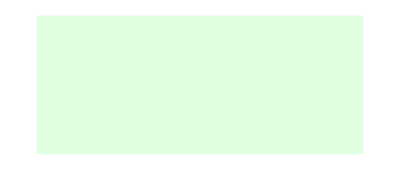

```mathematica
(*currently unused attempt to get the splines to show through the panle of locator points*)
Overlay[{Graphics[{LightGreen,Rectangle[{0,0},{400,170}]}],LocatorPane[Dynamic[{{x1,y1},{x4,y4},{x2,y2},{x3,y3},{x5,y5}}],splinePlotPanel1=Plot[splineP1[t],{t,0,3000}, AspectRatio-> 1/GoldenRatio, PlotRange-> {0,3000},PlotStyle->{Black,{Thickness[0.01]}},Axes->True,AxesLabel-> {"x","y"}, ImageSize->{300,150}]]
}]
```

## To Execute

```mathematica
(*places the locator points in a line from the beginning endpoint to the end*)
defaultPoints[];
```

```mathematica
(*default first screen*)
currentScreen=menu;
```

```mathematica
(*creates the game notebook*)
CreateDocument[Dynamic[currentScreen],WindowTitle-> "Roller Coaster Creator",Background-> LightBlue, WindowSelected->True,CellGrouping->Manual]
```

pvc_shm165FrontEndObject[LinkObject["pvc_shm", 3, 1]]165Roller Coaster Creator